## Preamble

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
```

## Test-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## Old-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## POLYNOMIAL REPRESENTATIONS OF S_n

## [ TBD ]

```mathematica
grp1=PermutationGroup[{Cycles[{{1,2}}],Cycles[{{2,3,4}}]}];
GroupOrder[grp1]
grp1
```

24

PermutationGroup[{Cycles[{{1,2}}],Cycles[{{2,3,4}}]}]

```mathematica
grp2=PermutationGroup[{Cycles[{{1,2}}],Cycles[{{1,2,3}}]}];
GroupOrder[grp2]
GroupElements[grp2]//TableForm
```

6

Cycles[{}]
Cycles[{{2,3}}]
Cycles[{{1,2}}]
Cycles[{{1,2,3}}]
Cycles[{{1,3,2}}]
Cycles[{{1,3}}]

```mathematica
FiniteGroupData[{"SymmetricGroup", 3},"Cycles"]
```

{{1},{2,1},{3,1},{4,5,1},{5,4,1},{6,1}}

```mathematica
(1+24/60+51/60^2+10/60^3)^2//N
```

2.

```mathematica
PrimeQ[127]
```

True

```mathematica
123456/7891011+1
```

2671489/2630337

```mathematica
Mod[1/5 ,7]
```

1/5

```mathematica
Grad[x^3+y^4+2 z^2+10,{x,y,z}]
Laplacian[x^3+y^4+2 z^2+10,{x,y,z}]
```

{3 x^2,4 y^3,4 z}

4+6 x+12 y^2

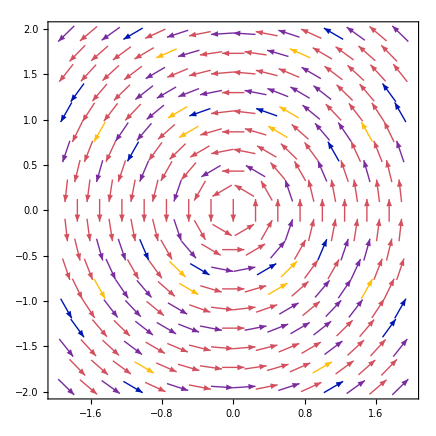

```mathematica
VectorPlot[{-y/(√(x^2+y^2)),x/(√(x^2+y^2))},{x,-2,2},{y,-2,2}]
```